```mathematica
(*This was similar to what I tried, I had it match the volume selected to the position in the list, but I coulnd't make it work.*)
```

```mathematica
Manipulate[
Module[{list,b,s},
list={5,4,3,2,1};
b=Position[list,a][[1,1]];
s=Rescale[b,{1,5}];
ColorData["TemperatureMap"][s]
],
Control[{{a,1,"position"},1,5,1,Appearance->"Labeled"}]
]
```

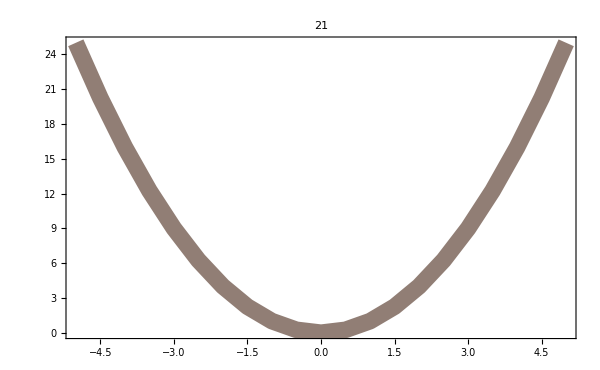

```mathematica
Module[{data},
data={#,#^2}&/@Range[-5,5,0.5];

ListPlot[data,Joined->True,PlotStyle->Thickness@0.02,
ColorFunction->(ColorData["Rainbow"][#1]&),
Axes->False,Frame->True,LabelStyle->{17,Black},ImageSize->600,PlotLabel->Length@data]
]
```

```mathematica
Manipulate[
Module[{data,s},
data={{0.00104,0.09733},{0.00106,0.19154},{0.00108,0.36001},{0.0011,0.61588},{0.00113,0.99936},{0.00116,1.55},{0.00119,2.313},{0.00123,3.338},{0.00128,4.681},{0.00133,6.402},{0.0014,8.57},{0.0015,11.26},{0.00164,14.57},{0.00189,18.63},{0.00248,21.77},{0.00311,22.06},{0.00349,22.04},{0.00642,19.32},{0.0102,15.13},{0.01473,11.72},{0.02066,8.938},{0.02876,6.697},{0.04018,4.913},{0.05675,3.518},{0.08163,2.449},{0.12012,1.65},{0.18215,1.07},{0.28662,0.66436},{0.4717,0.39165},{0.84388,0.2106},{1.57233,0.1083}};

s[x_]:=Rescale[Flatten@Position[data,x](*[[1,1]]*),{0,Length@data}];
ColorData["Rainbow"][s[data[[a,1]]]];
s[data[[a,1]]];
ListLogLogPlot[data,Joined->True,PlotStyle->Thickness@0.02,
(*ColorFunction->(ColorData["Rainbow"][s[#1]]&),*)
ColorFunction->(ColorData["Rainbow"][Position[data,#1]/Length@data]&),
ColorFunctionScaling->False,
Frame->True,ImageSize->600]
(*N@Rescale[Position[data,0.00133][[1,1]],{0,Length@data}]*)
],
Control[{{a,1,"position"},1,31,1,Appearance->"Labeled"}]
]
```

```mathematica
Length@{{0.00104,0.09733},{0.00106,0.19154},{0.00108,0.36001},{0.0011,0.61588},{0.00113,0.99936},{0.00116,1.55},{0.00119,2.313},{0.00123,3.338},{0.00128,4.681},{0.00133,6.402},{0.0014,8.57},{0.0015,11.26},{0.00164,14.57},{0.00189,18.63},{0.00248,21.77},{0.00311,22.06},{0.00349,22.04},{0.00642,19.32},{0.0102,15.13},{0.01473,11.72},{0.02066,8.938},{0.02876,6.697},{0.04018,4.913},{0.05675,3.518},{0.08163,2.449},{0.12012,1.65},{0.18215,1.07},{0.28662,0.66436},{0.4717,0.39165},{0.84388,0.2106},{1.57233,0.1083}}
```

31

```mathematica
Module[{PV,PV2},
PV={{0.00104,0.09733},{0.00105,0.13793},{0.00106,0.19154},{0.00107,0.26111},{0.00108,0.36001},{0.00109,0.47425},{0.0011,0.61588},{0.00111,0.78932},{0.00113,0.99936},{0.00114,1.2510},{0.00116,1.55},{0.00117,1.9020},{0.00119,2.313},{0.00121,2.789},{0.00123,3.338},{0.00125,3.966},{0.00128,4.681},{0.00130,5.49},{0.00133,6.402},{0.00137,7.426},{0.00140,8.57},{0.00145,9.845},{0.0015,11.260},{0.00156,12.830},{0.00164,14.570},{0.00174,16.5},{0.00189,18.63},{0.00216,20.76},{0.00248,21.77},{0.0028,22.04},{0.00311,22.060},{0.00311,22.060},{0.0034900,22.04},{0.00445,21.52},{0.00642,19.32},{0.00826,17.12},{0.0102,15.13},{0.01233,13.340},{0.014730,11.72},{0.017480,10.25},{0.02066,8.938},{0.024380,7.756},{0.02876,6.697},{0.03397,5.753},{0.04018,4.913},{0.04766,4.171},{0.05675,3.5180},{0.06789,2.946},{0.08163,2.449},{0.09872,2.019},{0.12012,1.65},{0.14732,1.336},{0.18215,1.07},{0.22732,0.84826},{0.28662,0.66436},{0.36536,0.51367},{0.47170,0.39165},{0.6169,0.29413},{0.84388,0.2106},{1.14142,0.15252},{1.57233,0.10830},{1.73732,0.09733}};

PV2=PV[[#]]&/@Range[1,Length@PV,2];

ListPlot[#,Joined->True,PlotStyle->Thick,Frame->True,ImageSize->450]&/@{PV,PV2};
PV2
]
```

{{0.00104,0.09733},{0.00106,0.19154},{0.00108,0.36001},{0.0011,0.61588},{0.00113,0.99936},{0.00116,1.55},{0.00119,2.313},{0.00123,3.338},{0.00128,4.681},{0.00133,6.402},{0.0014,8.57},{0.0015,11.26},{0.00164,14.57},{0.00189,18.63},{0.00248,21.77},{0.00311,22.06},{0.00349,22.04},{0.00642,19.32},{0.0102,15.13},{0.01473,11.72},{0.02066,8.938},{0.02876,6.697},{0.04018,4.913},{0.05675,3.518},{0.08163,2.449},{0.12012,1.65},{0.18215,1.07},{0.28662,0.66436},{0.4717,0.39165},{0.84388,0.2106},{1.57233,0.1083}}

```mathematica
{{0.00104,0.09733},{0.00106,0.19154},{0.00108,0.36001},{0.0011,0.61588},{0.00113,0.99936},{0.00116,1.55},{0.00119,2.313},{0.00123,3.338},{0.00128,4.681},{0.00133,6.402},{0.0014,8.57},{0.0015,11.26},{0.00164,14.57},{0.00189,18.63},{0.00248,21.77},{0.00311,22.06},{0.00349,22.04},{0.00642,19.32},{0.0102,15.13},{0.01473,11.72},{0.02066,8.938},{0.02876,6.697},{0.04018,4.913},{0.05675,3.518},{0.08163,2.449},{0.12012,1.65},{0.18215,1.07},{0.28662,0.66436},{0.4717,0.39165},{0.84388,0.2106},{1.57233,0.1083}}
```